```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/SMS-stop_SMQCD/SMS-stop_SMQCD",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
FR$ClassesTranslation
```

FR$ClassesTranslation

## Top Self Energy

### Remove diagrams which are identically zero due to color conservation

generic model {Lorentz} initialized

classes model {../Models/SMS-stop_SMQCD/SMS-stop_SMQCD} initialized

in total: 1 Particles insertion

in total: 1 Particles amplitude

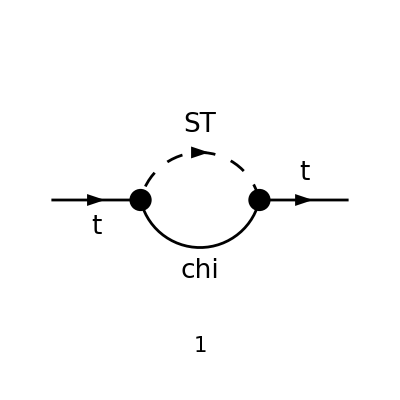

```mathematica
tops = CreateTopologies[1, 1->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
processTT =  { F[3]} -> {F[3]};
allDiags = InsertFields[tops,processTT, InsertionLevel-> {Particles},ExcludeParticles->{V[1]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->True,TransversePolarizationVectors->{p1,p2},DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[!M==={0},AppendTo[nonZero,n]];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

-((-ⅈ yDM (γ̄)^7 δ_Col1Col2).(mChi+γ·q).(-ⅈ yDM (γ̄)^6))/((q^2-mChi^2).((q-p)^2-mST^2))

```mathematica
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

(yDM^2 δ_Col1Col2 (γ·q).(γ̄)^6)/((q^2-mChi^2).((p-q)^2-mST^2))

```mathematica
ampC = TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify
```

-ⅈ π^2 yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 B_1(p^2,mChi^2,mST^2)

```mathematica
UVpart = DiracSimplify[PaXEvaluateUV[ampC]]
```

(ⅈ π^2 yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(2 ε_UV)

```mathematica
ampCeval=PaXEvaluate[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)]
```

-(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 (log(mChi^2/mST^2)-2 log(μ^2/mST^2)+2 ℽ-4-2 log(4 π)+4 log(π)+4 log(1/(2 π))+log(16)))/(64 π^2)+(ⅈ yDM^2 δ_Col1Col2 √(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4) (γ·p).(γ̄)^6 log((√(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4)+mChi^2+mST^2-p^2)/(2 mChi mST)))/(32 π^2 p^2)+(ⅈ yDM^2 (mChi-mST) (mChi+mST) δ_Col1Col2 √(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4) (γ·p).(γ̄)^6 log((√(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4)+mChi^2+mST^2-p^2)/(2 mChi mST)))/(32 π^2 p^4)+(ⅈ yDM^2 δ_Col1Col2 (mST^2 log(mChi^2/mST^2)+mChi^2-mST^2) (γ·p).(γ̄)^6)/(32 π^2 p^2)-(ⅈ yDM^2 (mChi-mST)^2 (mChi+mST)^2 δ_Col1Col2 log(mChi^2/mST^2) (γ·p).(γ̄)^6)/(64 π^2 p^4)+(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(32 π^2 ε)

```mathematica
FCClearScalarProducts[];
ScalarProduct[p,p]=MT^2;
```

```mathematica
ampCsimp=FullSimplify[SUNSimplify[FCTraceFactor[ampCeval]],Assumptions->{mST>0,mChi>0,MT>0}]
```

-1/(32 π^2 ε MT^4)ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 (ε MT^2 (mST^2-mChi^2)+ε (-2 mChi^2 mST^2+mChi^4+(mST^2-MT^2)^2) log(mChi/mST)+ε √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) (mChi^2-mST^2+MT^2) (log(2 mChi mST)-log(mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2))-ε MT^4 log((4 π μ^2)/mST^2)+((ℽ-2) ε-1) MT^4)

```mathematica
Collect[Limit[ampCsimp,mChi->mST],Epsilon]
```

(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(32 π^2 ε)-(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 (MT^4 (-log((4 π μ^2)/mST^2))+MT^2 √(MT^2 (-(2 mST-MT)) (2 mST+MT)) (log(2 mST^2)-log(2 mST^2+√(MT^2 (-(2 mST-MT)) (2 mST+MT))-MT^2))+(ℽ-2) MT^4))/(32 π^2 MT^4)

```mathematica
Collect[Limit[%,MT->0],Epsilon]
```

(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(32 π^2 ε)-(ⅈ yDM^2 δ_Col1Col2 (ℽ-log((4 π μ^2)/mST^2)) (γ·p).(γ̄)^6)/(32 π^2)

## Top - G - G vertex

generic model {Lorentz} initialized

classes model {../Models/SMS-stop_SMQCD/SMS-stop_SMQCD} initialized

in total: 1 Particles insertion

in total: 1 Particles amplitude

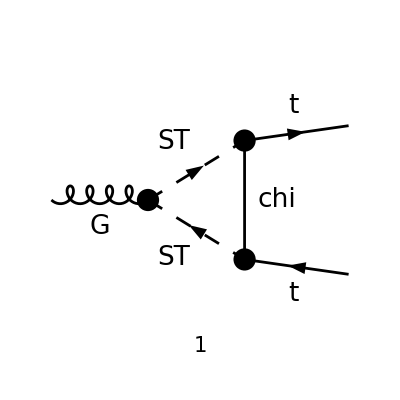

```mathematica
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[!M==={0},AppendTo[nonZero,n]];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames-> {μ,ν},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

(2 √π √aS T_Col2Col3^Glu1 (p1+p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(mChi+γ·(p1-q)).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((q-p1)^2-mChi^2).((-p1-p2+q)^2-mST^2))

```mathematica
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

-(2 √π √aS yDM^2 T_Col2Col3^Glu1 (p1^μ+p2^μ-2 q^μ) ((γ·p1).(γ̄)^6-(γ·q).(γ̄)^6))/((q^2-mST^2).((p1-q)^2-mChi^2).((p1+p2-q)^2-mST^2))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)
```

-2 ⅈ π^(5/2) √aS yDM^2 T_Col2Col3^Glu1 (2 γ^μ.(γ̄)^6 C_00(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+(p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 p1^μ (γ·p1).(γ̄)^6 C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-(p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_2(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 p2^μ (γ·p2).(γ̄)^6 C_22(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2))

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampC//Simplify
```

-2 ⅈ π^(5/2) √aS yDM^2 T_Col2Col3^Glu1 (2 γ^μ.(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+(p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-(p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 p1^μ (γ·p1).(γ̄)^6 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 p2^μ (γ·p2).(γ̄)^6 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2))

```mathematica
FullSimplify[Expand[PaXEvaluate[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries-> {{s,0,0},{MT,0,0}}]],Assumptions->{mST>0,mChi>0}]
```

1/(288 π^(3/2) ε (mChi-mST)^4 (mChi+mST)^4)ⅈ √aS yDM^2 T_Col2Col3^Glu1 (9 (mChi-mST)^2 (mChi+mST)^2 γ^μ.(γ̄)^6 ((mChi-mST) (mChi+mST) (mChi^2 (ε (-3+2 ℽ+log(1/(16 π^2)))-2)+2 ε (mST^2-mChi^2) log(μ^2/mST^2)+mST^2 (ε (1-2 ℽ+log(16)+2 log(π))+2))+4 ε mChi^4 log(mChi/mST))+ε ((γ·p1).(γ̄)^6 (p1^μ (9 mChi^4 mST^2+9 mChi^2 mST^4+12 mChi^4 (mChi^2+3 mST^2) log(mChi/mST)-17 mChi^6-mST^6)+p2^μ (27 mChi^4 mST^2-27 mChi^2 mST^4+12 mChi^4 (mChi^2-3 mST^2) log(mChi/mST)-5 mChi^6+5 mST^6))+(γ·p2).(γ̄)^6 (p1^μ (27 mChi^4 mST^2-27 mChi^2 mST^4+12 mChi^4 (mChi^2-3 mST^2) log(mChi/mST)-5 mChi^6+5 mST^6)+p2^μ (9 mChi^4 mST^2+9 mChi^2 mST^4+12 mChi^4 (mChi^2+3 mST^2) log(mChi/mST)-17 mChi^6-mST^6))))

```mathematica
Collect[%,{Epsilon,p1,p2}]
```

1/(288 π^(3/2) (mChi-mST)^4 (mChi+mST)^4)ⅈ √aS yDM^2 T_Col2Col3^Glu1 (18 (mChi-mST)^3 (mChi+mST)^3 (mST^2-mChi^2) γ^μ.(γ̄)^6 log(μ^2/mST^2)+(γ·p1).(γ̄)^6 (p1^μ (9 mChi^4 mST^2+9 mChi^2 mST^4+12 mChi^4 (mChi^2+3 mST^2) log(mChi/mST)-17 mChi^6-mST^6)+p2^μ (27 mChi^4 mST^2-27 mChi^2 mST^4+12 mChi^4 (mChi^2-3 mST^2) log(mChi/mST)-5 mChi^6+5 mST^6))+(γ·p2).(γ̄)^6 (p1^μ (27 mChi^4 mST^2-27 mChi^2 mST^4+12 mChi^4 (mChi^2-3 mST^2) log(mChi/mST)-5 mChi^6+5 mST^6)+p2^μ (9 mChi^4 mST^2+9 mChi^2 mST^4+12 mChi^4 (mChi^2+3 mST^2) log(mChi/mST)-17 mChi^6-mST^6))+36 mChi^4 (mChi-mST)^2 (mChi+mST)^2 γ^μ.(γ̄)^6 log(mChi/mST)+9 mChi^2 (-3+2 ℽ+log(1/(16 π^2))) (mChi-mST)^3 (mChi+mST)^3 γ^μ.(γ̄)^6+9 mST^2 (1-2 ℽ+log(16)+2 log(π)) (mChi-mST)^3 (mChi+mST)^3 γ^μ.(γ̄)^6)+(ⅈ √aS yDM^2 T_Col2Col3^Glu1 (18 mST^2 (mChi-mST)^3 (mChi+mST)^3 γ^μ.(γ̄)^6-18 mChi^2 (mChi-mST)^3 (mChi+mST)^3 γ^μ.(γ̄)^6))/(288 π^(3/2) ε (mChi-mST)^4 (mChi+mST)^4)

```mathematica
Limit[%,mChi->mST]
```

(ⅈ √aS yDM^2 T_Col2Col3^Glu1 (3 mST^2 γ^μ.(γ̄)^6 (2 ℽ ε-2 ε log(π)-ε log(16)-2 ε log(μ^2/mST^2)-2)+ε (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)))/(96 π^(3/2) ε mST^2)

```mathematica
Collect[%,Epsilon]
```

(ⅈ √aS yDM^2 T_Col2Col3^Glu1 (-6 mST^2 γ^μ.(γ̄)^6 log(μ^2/mST^2)+6 ℽ mST^2 γ^μ.(γ̄)^6-6 mST^2 log(π) γ^μ.(γ̄)^6-3 mST^2 log(16) γ^μ.(γ̄)^6+p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6))/(96 π^(3/2) mST^2)-(ⅈ √aS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(16 π^(3/2) ε)

```mathematica
Expand[%]
```

(ⅈ √aS yDM^2 p1^μ (γ·p2).(γ̄)^6 T_Col2Col3^Glu1)/(96 π^(3/2) mST^2)+(ⅈ √aS yDM^2 p2^μ (γ·p1).(γ̄)^6 T_Col2Col3^Glu1)/(96 π^(3/2) mST^2)-(ⅈ √aS yDM^2 γ^μ.(γ̄)^6 log(μ^2/mST^2) T_Col2Col3^Glu1)/(16 π^(3/2))-(ⅈ √aS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(16 π^(3/2) ε)+(ⅈ ℽ √aS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(16 π^(3/2))-(ⅈ √aS yDM^2 log(π) γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(16 π^(3/2))-(ⅈ √aS yDM^2 log(16) γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(32 π^(3/2))

```mathematica
FullSimplify[Expand[PaXEvaluate[PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},PaXEvaluate->True],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries-> {{s,0,0},{MT,0,0}}]],Assumptions->{mST>0,mChi>0}]
```

((mChi-mST) (mChi+mST) ((-2 ℽ ε+3 ε+2) mChi^2+2 ε (mChi-mST) (mChi+mST) log((4 π μ^2)/mST^2)+(2 ℽ ε-ε-2) mST^2)-4 ε mChi^4 log(mChi/mST))/(128 π^4 ε (mChi^2-mST^2)^2)

```mathematica
Collect[Expand[%],{Epsilon}]
```

(mChi^4/(64 π^4 (mChi^2-mST^2)^2)-(mChi^2 mST^2)/(32 π^4 (mChi^2-mST^2)^2)+mST^4/(64 π^4 (mChi^2-mST^2)^2))/ε+(mChi^4 log((4 π μ^2)/mST^2))/(64 π^4 (mChi^2-mST^2)^2)-(mChi^2 mST^2 log((4 π μ^2)/mST^2))/(32 π^4 (mChi^2-mST^2)^2)+(mST^4 log((4 π μ^2)/mST^2))/(64 π^4 (mChi^2-mST^2)^2)-(ℽ mChi^4)/(64 π^4 (mChi^2-mST^2)^2)+(3 mChi^4)/(128 π^4 (mChi^2-mST^2)^2)+(ℽ mChi^2 mST^2)/(32 π^4 (mChi^2-mST^2)^2)-(mChi^2 mST^2)/(32 π^4 (mChi^2-mST^2)^2)-(ℽ mST^4)/(64 π^4 (mChi^2-mST^2)^2)+mST^4/(128 π^4 (mChi^2-mST^2)^2)-(mChi^4 log(mChi/mST))/(32 π^4 (mChi^2-mST^2)^2)

```mathematica
Simplify[(%57/.{Epsilon->1/x}/.x->0)]
```

%57

```mathematica
FullSimplify[%,Assumptions->{mST>0,mChi>0}]
```

7.05703

```mathematica
Limit[%,mChi->mST]
```

(log((4 π μ^2)/mST^2)-ℽ)/(64 π^4)

```mathematica
UVpart = DiracSimplify[PaXEvaluateUV[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)]]
```

-(ⅈ √aS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(16 π^(3/2) ε_UV)

```mathematica
Expand[PaXEvaluate[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries-> {{s,0,0},{MT,0,0}}]]//Simplify
```

1/(288 π^(3/2) ε (mChi-mST)^4 (mChi+mST)^4)ⅈ √aS yDM^2 T_Col2Col3^Glu1 (9 (mChi^2-mST^2)^2 γ^μ.(γ̄)^6 (-3 ε mChi^4+2 ℽ ε mChi^4-2 ε mChi^4 log(π)-ε mChi^4 log(16)-2 ε (mChi^2-mST^2)^2 log(μ^2/mST^2)+4 ε mChi^2 mST^2-4 ℽ ε mChi^2 mST^2+2 ε mChi^4 log(mChi^2/mST^2)+4 ε mChi^2 mST^2 log(π)+ε mChi^2 mST^2 log(256)+4 mChi^2 mST^2-2 mChi^4-ε mST^4+2 ℽ ε mST^4-2 ε mST^4 log(π)-ε mST^4 log(16)-2 mST^4)+ε (-2 (18 mChi^4 mST^2-9 mChi^2 mST^4+6 mChi^6 log(mChi^2/mST^2)-11 mChi^6+2 mST^6) (p1^μ-2 p2^μ) (γ·p2).(γ̄)^6-9 (mChi^2-mST^2) (4 mChi^2 mST^2+2 mChi^4 log(mChi^2/mST^2)-3 mChi^4-mST^4) (p1^μ-p2^μ) (γ·(p1-p2)).(γ̄)^6+2 (18 mChi^4 mST^2-9 mChi^2 mST^4+6 mChi^6 log(mChi^2/mST^2)-11 mChi^6+2 mST^6) (2 p1^μ-p2^μ) (γ·p1).(γ̄)^6))

```mathematica
FullSimplify[SeriesCoefficient[%,{Epsilon,0,0}]]
```

1/(288 π^(3/2) (mChi^2-mST^2)^4)ⅈ √aS yDM^2 T_Col2Col3^Glu1 (9 (mChi-mST)^2 (mChi+mST)^2 γ^μ.(γ̄)^6 ((mChi-mST) (mChi+mST) (2 (mST^2-mChi^2) log((π μ^2)/mST^2)+mChi^2 (-3+2 ℽ-4 log(2))+mST^2 (1-2 ℽ+log(16)))+2 mChi^4 log(mChi^2/mST^2))+p1^μ (-9 (mChi-mST) (mChi+mST) (4 mChi^2 mST^2+2 mChi^4 log(mChi^2/mST^2)-3 mChi^4-mST^4) (γ·(p1-p2)).(γ̄)^6-2 (18 mChi^4 mST^2-9 mChi^2 mST^4+6 mChi^6 log(mChi^2/mST^2)-11 mChi^6+2 mST^6) (γ·p2).(γ̄)^6)+2 (18 mChi^4 mST^2-9 mChi^2 mST^4+6 mChi^6 log(mChi^2/mST^2)-11 mChi^6+2 mST^6) (2 p1^μ-p2^μ) (γ·p1).(γ̄)^6+p2^μ (9 (mChi-mST) (mChi+mST) (4 mChi^2 mST^2+2 mChi^4 log(mChi^2/mST^2)-3 mChi^4-mST^4) (γ·(p1-p2)).(γ̄)^6+4 (18 mChi^4 mST^2-9 mChi^2 mST^4+6 mChi^6 log(mChi^2/mST^2)-11 mChi^6+2 mST^6) (γ·p2).(γ̄)^6))

```mathematica
Limit[%,mChi->mST]
```

(ⅈ √aS yDM^2 T_Col2Col3^Glu1 (3 mST^2 γ^μ.(γ̄)^6 (-8 log((π μ^2)/mST^2)+8 ℽ-log(65536))-8 p1^μ (γ·(p1-p2)).(γ̄)^6-4 p1^μ (γ·p2).(γ̄)^6+(8 p1^μ-4 p2^μ) (γ·p1).(γ̄)^6+8 p2^μ (γ·(p1-p2)).(γ̄)^6+8 p2^μ (γ·p2).(γ̄)^6))/(384 π^(3/2) mST^2)

```mathematica
FullSimplify[%]
```

(ⅈ √aS yDM^2 T_Col2Col3^Glu1 (6 mST^2 γ^μ.(γ̄)^6 (ℽ-log((4 π μ^2)/mST^2))+p1^μ (2 (γ·p1).(γ̄)^6-2 (γ·(p1-p2)).(γ̄)^6-(γ·p2).(γ̄)^6)+p2^μ (2 ((γ·(p1-p2)).(γ̄)^6+(γ·p2).(γ̄)^6)-(γ·p1).(γ̄)^6)))/(96 π^(3/2) mST^2)

```mathematica
FullSimplify[SeriesCoefficient[%66,{Epsilon,0,-1}]]
```

-(ⅈ √aS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(16 π^(3/2))

## Top-Top - G - G vertex

generic model {Lorentz} initialized

classes model {../Models/SMS-stop_SMQCD/SMS-stop_SMQCD} initialized

in total: 3 Particles insertions

in total: 3 Particles amplitudes

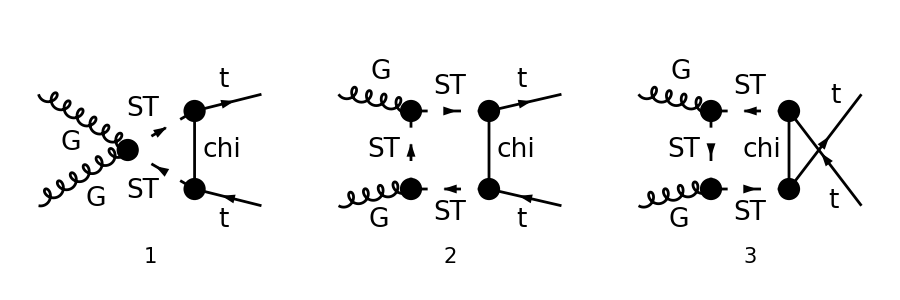

```mathematica
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGTT =  { V[1],V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[tops,processGGTT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],F[3]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[!M==={0},AppendTo[nonZero,n]];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{3,1},ImageSize->{ 900,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames-> {μ,ν},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 3 Particles amplitudes

(4 π aS (-k2-2 q)^ν T_Col3Col5^Glu2 T_Col5Col4^Glu1 (-k2+p1+p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(γ·(-k2+p1-q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+(4 π aS (-k2-2 q)^ν T_Col3Col5^Glu1 T_Col5Col4^Glu2 (-k2+p1+p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(γ·(k2-p2+q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-(4 π aS g^μν ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4) (-ⅈ yDM (γ̄)^7).(mChi-γ·q).(-ⅈ yDM (γ̄)^6))/((q^2-mChi^2).((p1+q)^2-mST^2).((q-p2)^2-mST^2))

## For this coupling we can assume on-shell gluons and tops

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[k1,k1]=0;
ScalarProduct[k2,k2]=0;
ScalarProduct[k1,k2]=s/2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

Also assume the gluons are have transverse polarization (on-shell gluons)

```mathematica
PT =1/2( MTD[μ,ν]-FVD[k1,ν]FVD[k2,μ]/ScalarProduct[k1,k2]);
```

```mathematica
ampB = Contract[PT SUNSimplify[FCTraceFactor[DiracSimplify[ampA]]]]//Simplify
```

-1/s 2 π aS yDM^2 ((γ·q).(γ̄)^6 (((D-1) s ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4))/((q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2))+2 (2 (k1·q) (k2·p1+k2·p2-2 (k2·q))+s (k2·q-p1·q-p2·q+2 q^2)) (((T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-((T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))))+2 (2 (k1·q) (k2·p1+k2·p2-2 (k2·q))+s (k2·q-p1·q-p2·q+2 q^2)) (-((γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+((γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+(γ·k2).(γ̄)^6 (((T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-((T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2)))))

```mathematica
ampC = TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify
```

1/s 2 ⅈ aS π^3 yDM^2 (s C_0(MT^2,0,MT^2-2 (k2·p2),mChi^2,mST^2,mST^2) (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4+(4 mST^2-s) s D_0(MT^2,MT^2,0,s-2 (k2·p1)-2 (k2·p2),s,MT^2-2 (k2·p2),mST^2,mChi^2,mST^2,mST^2) (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4-2 C_0(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (γ·p1).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) (T^Glu1 T^Glu2)_Col3Col4+s (γ·k2).(γ̄)^6 C_1(0,MT^2-2 (k2·p2),MT^2,mST^2,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col3Col4-2 (γ·p1).(γ̄)^6 (s-4 (k1·p1)-2 (k1·p2)) C_1(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-s ((s-4 mST^2) (γ·k2).(γ̄)^6+2 (γ·p2).(γ̄)^6 (k2·p1+k2·p2)) D_1(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+s (γ·p2).(γ̄)^6 C_2(0,MT^2-2 (k2·p2),MT^2,mST^2,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col3Col4-2 ((γ·p1).(γ̄)^6+(-(γ·(k2-p1-p2))).(γ̄)^6) (s-2 (k1·p1)-2 (k1·p2)) C_2(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+(γ·p2).(γ̄)^6 ((4 mST^2-s) s-4 (k1·p2) (k2·p1+k2·p2)) D_2(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-((4 mST^2-s) s (-(γ·(p1+p2))).(γ̄)^6+4 (γ·p2).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2)) D_3(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (γ·k1).(γ̄)^6 C_00(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·k1).(γ̄)^6 (k2·p1+k2·p2) D_00(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (γ·p1).(γ̄)^6 (k1·p1) C_11(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 s (γ·k2).(γ̄)^6 (k2·p1+k2·p2) D_11(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 ((γ·p1).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2))-2 (-(γ·(k2-p1-p2))).(γ̄)^6 (k1·p1)) C_12(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (s (γ·p2).(γ̄)^6+2 (γ·k2).(γ̄)^6 (k1·p2)) (k2·p1+k2·p2) D_12(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 (s (-(γ·(p1+p2))).(γ̄)^6-2 (γ·k2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_13(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (-(γ·(k2-p1-p2))).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_22(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·p2).(γ̄)^6 (k1·p2) (k2·p1+k2·p2) D_22(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 ((γ·p2).(γ̄)^6 (k1·p1+k1·p2)-(-(γ·(p1+p2))).(γ̄)^6 (k1·p2)) (k2·p1+k2·p2) D_23(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (-(γ·(p1+p2))).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2) D_33(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·k1).(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)-4 ((γ·p1).(γ̄)^6 (k1·p1)+(γ·p2).(γ̄)^6 (k1·p2)) C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)+4 ((γ·p2).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (k1·p2)) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)-s C_0(MT^2,0,MT^2-2 (k2·p1),mChi^2,mST^2,mST^2) (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4-(4 mST^2-s) s D_0(MT^2,MT^2,0,s-2 (k2·p1)-2 (k2·p2),s,MT^2-2 (k2·p1),mST^2,mChi^2,mST^2,mST^2) (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4+2 C_0(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (γ·p2).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) (T^Glu2 T^Glu1)_Col3Col4-s (γ·k2).(γ̄)^6 C_1(0,MT^2-2 (k2·p1),MT^2,mST^2,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col3Col4+2 (γ·p2).(γ̄)^6 (s-2 (k1·p1)-4 (k1·p2)) C_1(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+s ((s-4 mST^2) (γ·k2).(γ̄)^6+2 (γ·p1).(γ̄)^6 (k2·p1+k2·p2)) D_1(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-s (γ·p1).(γ̄)^6 C_2(0,MT^2-2 (k2·p1),MT^2,mST^2,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col3Col4+2 ((-(γ·(k2-p1-p2))).(γ̄)^6+(γ·p2).(γ̄)^6) (s-2 (k1·p1)-2 (k1·p2)) C_2(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-(γ·p1).(γ̄)^6 ((4 mST^2-s) s-4 (k1·p1) (k2·p1+k2·p2)) D_2(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+((4 mST^2-s) s (-(γ·(p1+p2))).(γ̄)^6+4 (γ·p1).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2)) D_3(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (γ·k1).(γ̄)^6 C_00(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·k1).(γ̄)^6 (k2·p1+k2·p2) D_00(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (γ·p2).(γ̄)^6 (k1·p2) C_11(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 s (γ·k2).(γ̄)^6 (k2·p1+k2·p2) D_11(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 ((γ·p2).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2))-2 (-(γ·(k2-p1-p2))).(γ̄)^6 (k1·p2)) C_12(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 (s (γ·p1).(γ̄)^6+2 (γ·k2).(γ̄)^6 (k1·p1)) (k2·p1+k2·p2) D_12(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 (s (-(γ·(p1+p2))).(γ̄)^6-2 (γ·k2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_13(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 (-(γ·(k2-p1-p2))).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_22(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·p1).(γ̄)^6 (k1·p1) (k2·p1+k2·p2) D_22(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 ((γ·p1).(γ̄)^6 (k1·p1+k1·p2)-(-(γ·(p1+p2))).(γ̄)^6 (k1·p1)) (k2·p1+k2·p2) D_23(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (-(γ·(p1+p2))).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2) D_33(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6) C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((4 (k1·p2)-(D-2) s) (T^Glu1 T^Glu2)_Col3Col4+(4 (k1·p1)-(D-2) s) (T^Glu2 T^Glu1)_Col3Col4))

```mathematica
SUNSimplify[%]
```

1/s 2 ⅈ aS π^3 yDM^2 (s C_0(MT^2,0,MT^2-2 (k2·p2),mChi^2,mST^2,mST^2) (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4+(4 mST^2-s) s D_0(MT^2,MT^2,0,s-2 (k2·p1)-2 (k2·p2),s,MT^2-2 (k2·p2),mST^2,mChi^2,mST^2,mST^2) (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4-2 C_0(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (γ·p1).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) (T^Glu1 T^Glu2)_Col3Col4+s (γ·k2).(γ̄)^6 C_1(0,MT^2-2 (k2·p2),MT^2,mST^2,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col3Col4+((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6) (4 (k1·p2)-(D-2) s) C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (γ·p1).(γ̄)^6 (s-4 (k1·p1)-2 (k1·p2)) C_1(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-s ((s-4 mST^2) (γ·k2).(γ̄)^6+2 (γ·p2).(γ̄)^6 (k2·p1+k2·p2)) D_1(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+s (γ·p2).(γ̄)^6 C_2(0,MT^2-2 (k2·p2),MT^2,mST^2,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col3Col4-2 (γ·p1-γ·(k2-p1-p2)).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_2(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+(γ·p2).(γ̄)^6 ((4 mST^2-s) s-4 (k1·p2) (k2·p1+k2·p2)) D_2(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-(4 (γ·p2).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2)-(4 mST^2-s) s (γ·(p1+p2)).(γ̄)^6) D_3(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·k1).(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (γ·k1).(γ̄)^6 C_00(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·k1).(γ̄)^6 (k2·p1+k2·p2) D_00(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 ((γ·p1).(γ̄)^6 (k1·p1)+(γ·p2).(γ̄)^6 (k1·p2)) C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (γ·p1).(γ̄)^6 (k1·p1) C_11(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 s (γ·k2).(γ̄)^6 (k2·p1+k2·p2) D_11(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 ((γ·p2).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (k1·p2)) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (2 (γ·(k2-p1-p2)).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2))) C_12(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (s (γ·p2).(γ̄)^6+2 (γ·k2).(γ̄)^6 (k1·p2)) (k2·p1+k2·p2) D_12(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 (-s (γ·(p1+p2)).(γ̄)^6-2 (γ·k2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_13(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 (γ·(k2-p1-p2)).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_22(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·p2).(γ̄)^6 (k1·p2) (k2·p1+k2·p2) D_22(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 ((γ·(p1+p2)).(γ̄)^6 (k1·p2)+(γ·p2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_23(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·(p1+p2)).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2) D_33(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-s C_0(MT^2,0,MT^2-2 (k2·p1),mChi^2,mST^2,mST^2) (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4-(4 mST^2-s) s D_0(MT^2,MT^2,0,s-2 (k2·p1)-2 (k2·p2),s,MT^2-2 (k2·p1),mST^2,mChi^2,mST^2,mST^2) (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4+2 C_0(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (γ·p2).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) (T^Glu2 T^Glu1)_Col3Col4-s (γ·k2).(γ̄)^6 C_1(0,MT^2-2 (k2·p1),MT^2,mST^2,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col3Col4+((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6) (4 (k1·p1)-(D-2) s) C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 (γ·p2).(γ̄)^6 (s-2 (k1·p1)-4 (k1·p2)) C_1(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+s ((s-4 mST^2) (γ·k2).(γ̄)^6+2 (γ·p1).(γ̄)^6 (k2·p1+k2·p2)) D_1(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-s (γ·p1).(γ̄)^6 C_2(0,MT^2-2 (k2·p1),MT^2,mST^2,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col3Col4+2 (γ·p2-γ·(k2-p1-p2)).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_2(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-(γ·p1).(γ̄)^6 ((4 mST^2-s) s-4 (k1·p1) (k2·p1+k2·p2)) D_2(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+(4 (γ·p1).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2)-(4 mST^2-s) s (γ·(p1+p2)).(γ̄)^6) D_3(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·k1).(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (γ·k1).(γ̄)^6 C_00(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·k1).(γ̄)^6 (k2·p1+k2·p2) D_00(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 ((γ·p1).(γ̄)^6 (k1·p1)+(γ·p2).(γ̄)^6 (k1·p2)) C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (γ·p2).(γ̄)^6 (k1·p2) C_11(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 s (γ·k2).(γ̄)^6 (k2·p1+k2·p2) D_11(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 ((γ·p2).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (k1·p2)) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 ((γ·p2).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2))+2 (γ·(k2-p1-p2)).(γ̄)^6 (k1·p2)) C_12(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 (s (γ·p1).(γ̄)^6+2 (γ·k2).(γ̄)^6 (k1·p1)) (k2·p1+k2·p2) D_12(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 (-s (γ·(p1+p2)).(γ̄)^6-2 (γ·k2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_13(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 (γ·(k2-p1-p2)).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_22(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·p1).(γ̄)^6 (k1·p1) (k2·p1+k2·p2) D_22(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 ((γ·(p1+p2)).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_23(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·(p1+p2)).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2) D_33(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4)

```mathematica
UVpart = DiracSimplify[PaXEvaluateUV[ampC]]
```

0